```mathematica
ExpandAll[1/l∫_-l^l (x^3 - 2 x^2)Cos[(n π x)/l]ⅆx]
```

-(8 l^2 Cos[n π])/(n^2 π^2)+(8 l^2 Sin[n π])/(n^3 π^3)-(4 l^2 Sin[n π])/(n π)

```mathematica
ExpandAll[1/l∫_-l^l (x^3 - 2 x^2)ⅆx]
```

-(4 l^2)/3

```mathematica
w := 3
```

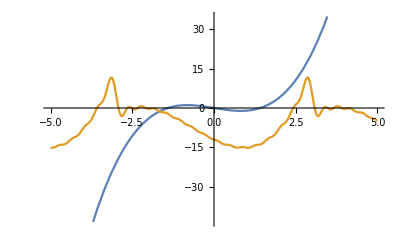

```mathematica
Plot[{x^3-2x, 1/2(-(4 w^2)/3) + ∑_(n=1)^15 (((-1)^n 8 w^2)/(n π)^2 Cos[(n π x)/w] + (((-1)^n 12 w^3)/(n π)^3 - ((-1)^n 2 w^2)/(n π))Sin[(n π x)/w])}, {x, -5, 5}]
```

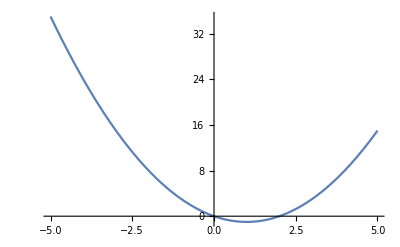

```mathematica
Plot[x^2 - 2 x, {x, -5, 5}]
```

```mathematica
ExpandAll[1/l∫_-l^l (x^2-2x)Cos[(n π x)/l]ⅆx]
```

(4 l^2 Cos[n π])/(n^2 π^2)-(4 l^2 Sin[n π])/(n^3 π^3)+(2 l^2 Sin[n π])/(n π)

```mathematica
ExpandAll[∫(x^2-2x)ⅆx]
```

-x^2+x^3/3

```mathematica
(-l)^3
```

-l^3

```mathematica
ExpandAll[1/l∫_-l^l (x^2-2x)Sin[(n π x)/l]ⅆx]
```

(4 l Cos[n π])/(n π)-(4 l Sin[n π])/(n^2 π^2)

5

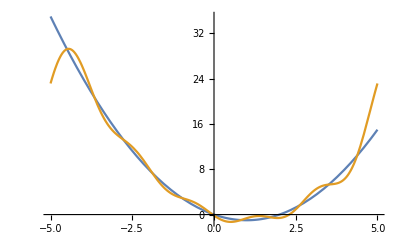

```mathematica
w = 5
Plot[
{x^2 - 2 x,
1/2(2/3 w^2) + ∑_(n=1)^5 ((-1)^n*(4 w^2)/(n π)^2*Cos[(n π x)/w] + (-1)^n*(4 w)/(n π)*Sin[(n π x)/w])
},

 {x, -5, 5}]
```

5

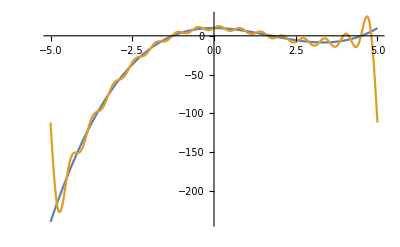

```mathematica
w = 5
Plot[
{x^3 - 5 x^2+10,
10+1/2(-10/3 w^2) + ∑_(n=1)^15 ((-1)^n*(-20 w^2)/(n π)^2*Cos[(n π x)/w] + (-1)^n*(12(w/(n π))^3-2*w^3/(n π))*Sin[(n π x)/w])
},

 {x, -5, 5}]
```

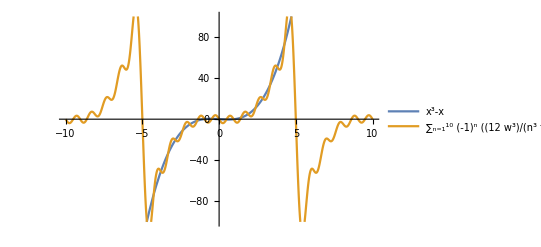

```mathematica
Plot[
{x^3-x,
∑_(n=1)^10 (-1)^n((12 w^3)/(n^3 π^3) + (2w - 2 w^3)/(n π))Sin[(n π x)/w]
},
{x, -10, 10}, PlotLegends->"Expressions", PlotRange-> {-100, 100}]
```